```mathematica
PRAVOKOTNIK,KVADER, KVADRAT, KOCKA
```

```mathematica
*PRAVOKOTNIK IN KVADER
```

```mathematica
Obseg pravokotnika: 2a+2b
Ploščina pravokotnika: a*b
```

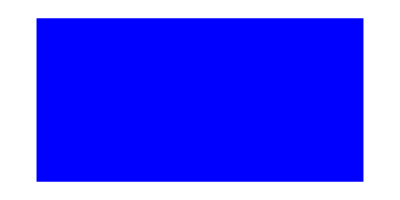

```mathematica
Graphics[{Blue,Rectangle[{2,1},{4,2}]}]
```

```mathematica
Površina kvadra: 2(ab+ac+bc)
Volmen kvadra: a*b*c
```

```mathematica
število:=RandomReal[1.,{3}]
kvader:=Polygon[Table[število,{3}]]
Graphics3D[kvader]
```

-Graphics3D-

```mathematica
Risanje grafov - pravokotniki:
```

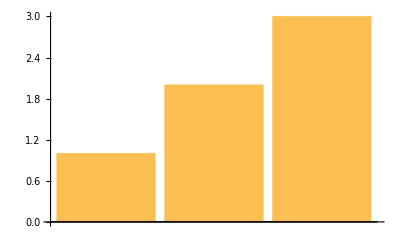

```mathematica
RectangleChart[{{1,1},{1,2},{1,3}}]
```

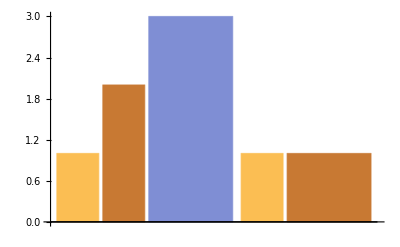

```mathematica
RectangleChart[{{{1,1},{1,2},{2,3}},{{1,1},{2,1}}}]
```

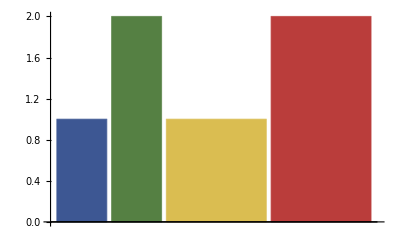

```mathematica
RectangleChart[Tuples[{1,2},2],ChartStyle->"DarkRainbow"]
```

```mathematica
Zaokroženi pravokotniki:
```

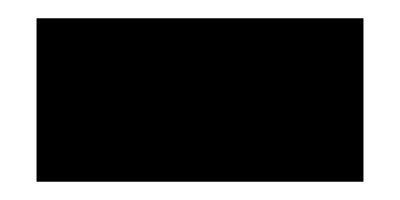

```mathematica
Graphics[Rectangle[{0,0},{2,1},RoundingRadius->0.3]]
```

```mathematica
Framed[1/ROM+y+z,RoundingRadius->10]
```

1/ROM+y+z

```mathematica
3D oblike:
```

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0},{1,3,1}],Blue,Cuboid[{2,1,1},{4,2,3}]}]
```

-Graphics3D-

```mathematica
Graphics3D[Table[kvader,{5}]]
```

-Graphics3D-

```mathematica
*KVADRAT IN KOCKA
```

```mathematica
Obseg kvadrata: 4*a
```

```mathematica
Ploščina kvadrata: a^2
```



```mathematica
Graphics[Rectangle[]]
```

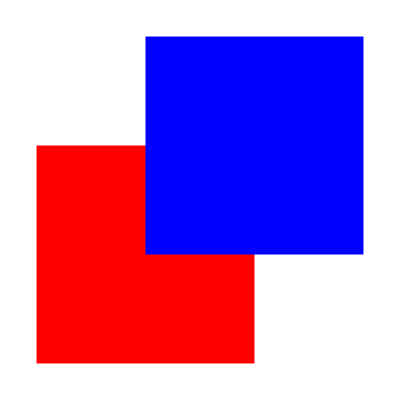

```mathematica
Graphics[{Red,Rectangle[{0,0}],Blue,Rectangle[{0.5,0.5}]}]
```

```mathematica
RadialGradientImage[{Blue,Yellow,Red}]
```

-Graphics-

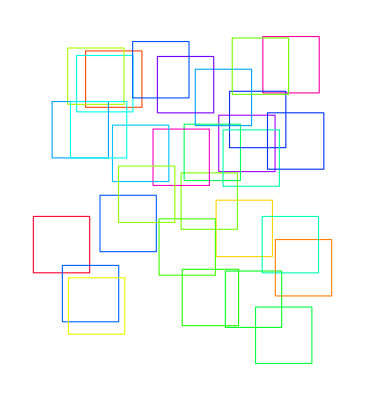

```mathematica
Graphics[{EdgeForm[{Thick,Hue[Random[]]}],FaceForm[],Rectangle[#,#+{4,4}]}&/@RandomReal[{-10,10},{30,2}]]
```

```mathematica
Površina kocke:6*a^2
Prostornina kocke: a^3
```

```mathematica
Graphics3D[Cuboid[]]
```

-Graphics3D-

```mathematica
cub=Graphics3D[{Cuboid[{0,0,0}],Cuboid[{0,0,1}],Cuboid[{0,1,1}],Cuboid[{1,1,1}],{SurfaceColor[RGBColor[0,1,0]],Cuboid[{1.25,0.25,0.25},{1.75,0.75,0.75}]}}];
cub
```

-Graphics3D-

```mathematica
Graphics3D[{Hue[#],Cuboid[#,#+.1]}&/@Tuples[Range[0,1,.2],3],Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0}],Blue,Cuboid[{0.5,0.5,0.5}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{Glow[Purple],Cylinder[]},Lighting->None]
```

-Graphics3D-

```mathematica
Graphics3D[Polygon[Table[{Cos[2 π k/5],Sin[2 π k/5],0},{k,0,8,2}]]]
```

-Graphics3D-

```mathematica
Table[Graphics3D[{Yellow,Opacity[.8],PolyhedronData[p,"GraphicsComplex"]}],{p,{"Dodecahedron","Icosahedron","TruncatedIcosahedron"}}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-}